```mathematica
Remove["Global`*"]


ohm=Piecewise[{{0.01*Exp[-((x-1000)/250)^2],x>500&&x<1500},{E^(-4)*0.01,x>1500}},E^(-4)*0.01]
logk=Log[k];
```

Piecewise[{{0.01 ⅇ^(-(-1000+x)^2/62500), x>500&&x<1500}, {0.000183156, True}}]

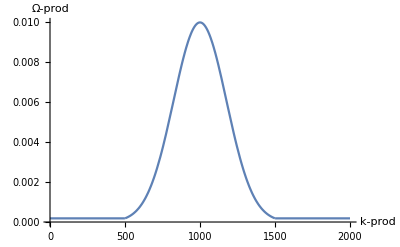

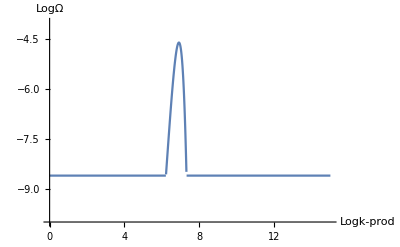

```mathematica
Plot[ohm,{x,0,2000},AxesLabel->{k -prod,Ω-prod},PlotRange->Automatic]
x=Exp[logx];
omega=Log[ohm];
Plot[omega,{logx,0,15},PlotRange->{-10,-4},AxesLabel->{Logk-prod,LogΩ}]
```

```mathematica
loga=-0*logk;
```

```mathematica
c=1;
```

```mathematica
logkk=logk-loga+c
```

1+Log[k]

```mathematica
f=Log[Ω[Exp[logkk]]]
```

Log[Ω[ⅇ k]]

```mathematica
logΩ=2*(logk+loga+c)*f
```

2 (1+Log[k]) Log[Ω[ⅇ k]]

```mathematica
Plot[logΩ,{logk,0,10},AxesLabel->{logk,logΩ}]
```

-Graphics-